## Neural Networks

### predict a number from numbers

#### 1 prepare datasets

```mathematica
Batch[n_]:=Thread[#->{Plus@@#}&/@RandomInteger[10,{n,2}]]
```

```mathematica
dataT=Batch@300;
dataV=Batch@10;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{2,Ramp,1},"Input"->{2},"Output"->{1}]
```

NetChain[<>]

```mathematica
net[{3,4}]
```

{0.117218}

```mathematica
NetExtract[net,{1,"Weights"}]//Normal
```

{{-0.811653,0.691436},{0.330808,-0.107259}}

what is a linear layer?

```mathematica
linear=NetInitialize@LinearLayer[5,"Input"->{3}]
```

LinearLayer[<>]

```mathematica
linear[{.1,.2,.3}]
```

{0.110566,0.0208071,0.106751,0.128839,0.0422248}

or extract it from the net model, the first layer has two node

```mathematica
NetExtract[net,1]
```

LinearLayer[<>]

```mathematica
NetExtract[net,1]@{3,4}
```

{0.330784,0.563386}

#### 3 train and validate

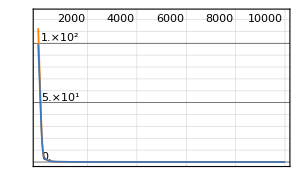
NetTrain Results
summary | ,,  batches:20000  rounds:10000  time:30s  examples/s:43443
data | ,,  training examples:100  validation examples:10  processed examples:1280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.55×10^-6
validation | ,,  loss:6.4×10^-6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV]
```

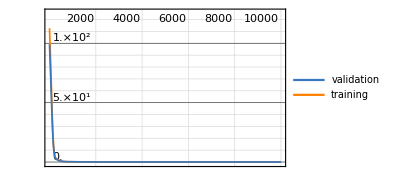
| rounds
loss | -Graphics-

<|Loss→8.54611×10^-6|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=4
dataV[[n]]
net[dataV[[n,1]]]
netF[dataV[[n,1]]]
```

4

{7,0}→{7}

{0.302342}

{7.}

```mathematica
NetExtract[NetExtract[netF,1],"Weights"]//Normal
```

{{0.0163453,1.20692},{1.19319,0.397848}}

### assigning a class to a number

#### 1 prepare datasets

```mathematica
Batch[n_]:=Replace[RandomInteger[{-10,10},{n,1}],{{a_/;a>0}:>({a}->"PLUS"),{a_/;a<0}:>({a}->"MINUS"),{a_/;a==0}:>({a}->"ZERO")},All]
```

```mathematica
Batch@3
```

{{-5}→MINUS,{2}→PLUS,{-6}→MINUS}

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{6,Ramp,3,SoftmaxLayer[]},"Input"->{1},"Output"->NetDecoder[{"Class",{"PLUS","MINUS","ZERO"}}]]
```

NetChain[<>]

```mathematica
NetExtract[net,4][{-0.24748778343200684,-0.3324894607067108,0.09656712412834167}]
```

{0.300375,0.275898,0.423726}

```mathematica
NetTake[net,3][{4}]
```

{-0.247488,-0.332489,0.0965671}

```mathematica
NetExtract[net,"Output"][{0.30037546157836914,0.2758980989456177,0.42372646927833557}]
```

ZERO

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

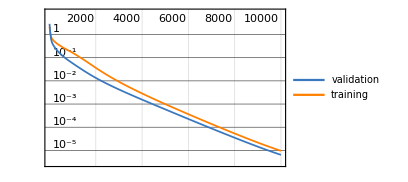
| rounds
loss | -Graphics-

<|Loss→9.58018×10^-6,ErrorRate→0.|>

NetChain[<>]

1.

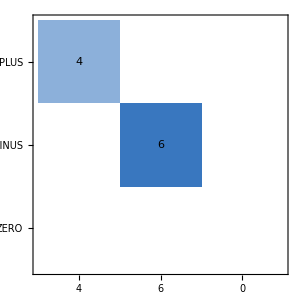
actual class | -Graphics-
 | predicted class

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
NetMeasurements[netF,dataV,"Accuracy"]
NetMeasurements[netF,dataV,"ConfusionMatrixPlot"]
```

```mathematica
netF[{0}]
```

ZERO

```mathematica
netF[{2},"Probabilities"]
```

<|PLUS→0.999984,MINUS→7.24973×10^-6,ZERO→8.84118×10^-6|>

### assigning a class to number 2

#### 1 prepare datasets

```mathematica
Batch[n_]:=Module[{makeCluster},makeCluster[class_,μ_,ρ_]:=RandomVariate[MultinormalDistribution[μ,{{1,2ρ},{2ρ,4}}],Round[n/3]]->class;
Flatten[Thread/@makeCluster@@@{{Red,{1.5,1.5},-.2},{Green,{-1.5,1},.1},{Blue,{0,-2.5},.8}}]]
```

```mathematica
Batch@3
```

{{0.17491,1.29701}→RGBColor[1, 0, 0],{-2.18862,4.90798}→RGBColor[0, 1, 0],{-1.94606,-5.03265}→RGBColor[0, 0, 1]}

```mathematica
dataT=Batch@600;
dataV=Batch@60;
```

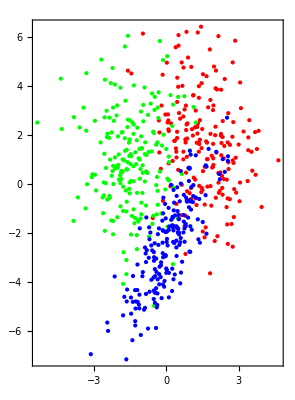

```mathematica
gr=Graphics[Cases[dataT,(a_->b_):>{b,Point@a},1],PlotRange->5,Frame->True]
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{30,Ramp,3,SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green,Blue}}]]
```

NetChain[<>]

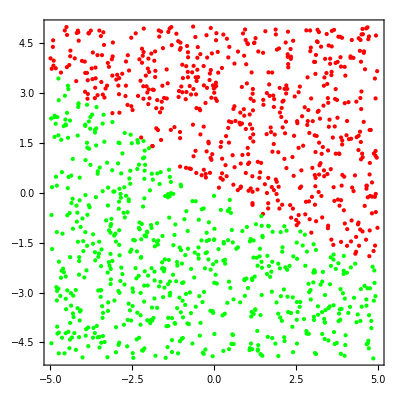

```mathematica
Graphics[{net@#,Point@#}&/@RandomReal[{-5,5},{1200,2}],Frame->True]
```

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

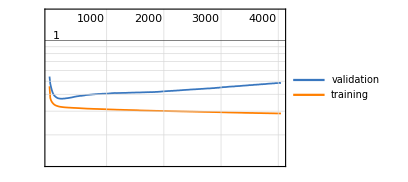
| rounds
loss | -Graphics-

<|Loss→0.288185,ErrorRate→0.129688|>

NetChain[<>]

0.883333

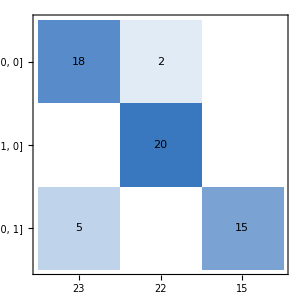
actual class | -Graphics-
 | predicted class

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
NetMeasurements[netF,dataV,"Accuracy"]
NetMeasurements[netF,dataV,"ConfusionMatrixPlot"]
```

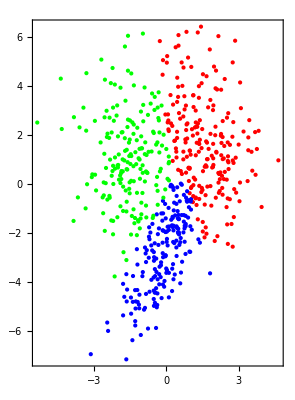

```mathematica
Graphics[Cases[dataT,(a_->b_):>{netF@a,Point@a},1],PlotRange->5,Frame->True]
```

0.5

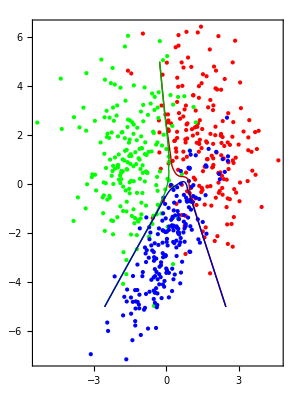

```mathematica
probability=0.5
Show[gr,Quiet@Table[ContourPlot[netF[{x,y},{"Probability",color}]==probability,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green,Blue}}]]
```

### predict an image from image

#### 1 prepare datasets

```mathematica
Options[imageCreate]={"Color"->Black,"Size"->.1,"Shape"->"Point","Filter"->0};
imageCreate[pt_,OptionsPattern[]]:=Module[{size=OptionValue@"Size",color=OptionValue@"Color"},GaussianFilter[ColorConvert[Rasterize[Graphics[{{LightGray,Rectangle[]},Switch[OptionValue@"Shape","Rect",{color,Rectangle[pt-{size,size},pt+{size,size}]},"Disk",{color,Disk[pt,size]},_,{color,PointSize@size,Point[pt]}]},Frame->False,ImageSize->32]],"RGB"],OptionValue@"Filter"]]
```

```mathematica
$status=0;
Batch[n_]:=Module[{},
imageCreate[$status++;
RandomReal[{.2,.8},2],"Size"->.15,"Shape"->#]->imageCreate[{.5,.5},"Size"->Switch[#,"Rect",.1,"Disk",.2],"Shape"->#]&/@RandomChoice[{"Rect","Disk"},n]]
```

```mathematica
Batch@3
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Dynamic@$status
dataT=Batch@100;
dataV=Batch@10;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
FlattenLayer[],
LinearLayer[784],
Tanh,
ReshapeLayer[{1,28,28}]},
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}],
"Output"->NetDecoder[{"Image","Grayscale"}]]
```

NetChain[<>]

```mathematica
nec=NetEncoder[{"Image",{28,28},"Grayscale"}]
```

NetEncoder[<>]

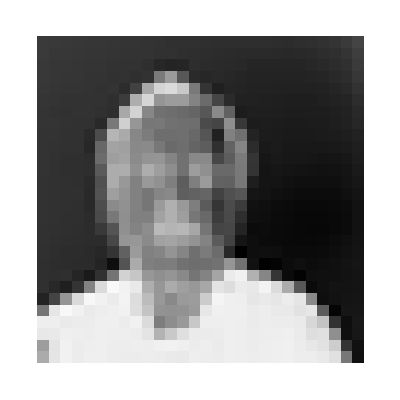

```mathematica
ArrayReshape[nec@-Graphics-,{28,28}]//ArrayPlot
```

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

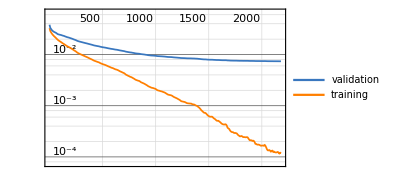
| rounds
loss | -Graphics-

<|Loss→0.000117198|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
dataV[[8]]
netF@%[[1]]
```

-Graphics-→-Graphics-

-Graphics-

### predict a vector from images (convolutional encoder)

#### 1 prepare datasets

```mathematica
Batch[n_]:=Module[{},
imageCreate[$status++;#,"Size"->RandomReal[{.05,.15}],"Color"->RandomColor[],"Shape"->RandomChoice[{"Rect","Disk"}]]->#]&/@RandomReal[{.1,.9},{n,2}]
```

```mathematica
Batch@3
```

{-Graphics-→{0.60592,0.358815},-Graphics-→{0.564972,0.757383},-Graphics-→{0.210607,0.453756}}

```mathematica
$status=0;
Dynamic@$status
dataT=Batch@500;
dataV=Batch@50;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[120],
ElementwiseLayer[Ramp],
LinearLayer[2]},
"Input"->NetEncoder[{"Image",{28,28},"RGB"}],
"Output"->{2}]
```

NetChain[<>]

```mathematica
net@dataV[[1,1]]
```

{-1.05109,0.797394}

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV,MaxTrainingRounds->100];
```

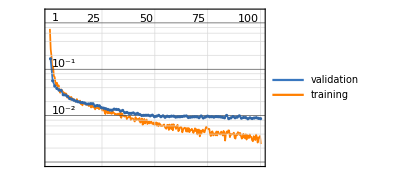
| rounds
loss | -Graphics-

<|Loss→0.00326248|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
dataV[[2]]
netF@%[[1]]
```

-Graphics-→{0.538608,0.799265}

{0.556554,0.906659}

```mathematica
StringLength@Compress@netF
```

251298

```mathematica
n=9;
dataV[[n,2]]
netF@dataV[[n,1]]
HighlightImage[dataV[[n,1]],{AbsolutePointSize[6],Opacity@1,Red,netF@dataV[[n,1]]32}]
```

{0.612637,0.362752}

{0.446213,0.391207}

-Graphics-

### specify a morphology character from images (convolutional classifier)

#### 1 prepare datasets

```mathematica
Batch[n_]:=Module[{},imageCreate[$status++;RandomReal[{.2,.8},2],"Size"->RandomReal[{.1,.2}],"Color"->RandomColor[],"Shape"->#]->#]&/@RandomChoice[{"Rect","Disk"},n]
```

```mathematica
Batch@3
```

{-Graphics-→Rect,-Graphics-→Disk,-Graphics-→Disk}

```mathematica
$status=0;
Dynamic@$status
dataT=Batch@1000;
dataV=Batch@100;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[120],
ElementwiseLayer[Ramp],
LinearLayer[2],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Image",{28,28},"RGB"}],
"Output"->NetDecoder[{"Class",{"Rect","Disk"}}]]
```

NetChain[<>]

```mathematica
dataV[[1]]
net@dataV[[1,1]]
```

-Graphics-→Disk

Disk

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV,MaxTrainingRounds->100];
```

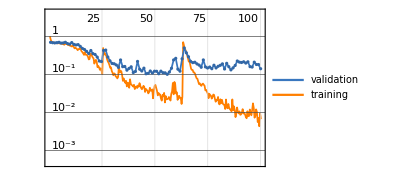
| rounds
loss | -Graphics-

<|Loss→0.006918,ErrorRate→0.00292969|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
dataV[[8]]
netF@%[[1]]
```

-Graphics-→Disk

Disk

```mathematica
dataV[[8]]
netF[%[[1]],"Probabilities"]
```

-Graphics-→Disk

<|Rect→0.0000124719,Disk→0.999988|>

```mathematica
ClassifierMeasurements[netF,dataV,"WorstClassifiedExamples"]
```

{-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Rect,-Graphics-→Disk}

```mathematica
ClassifierMeasurements[netF,dataV,"MisclassifiedExamples"]
```

{-Graphics-→Disk,-Graphics-→Rect,-Graphics-→Disk,-Graphics-→Rect}

### predict the next character (RNN)

#### 1 prepare datasets

```mathematica
seq=StringJoin@Array["abcd"&,6]
```

abcdabcdabcdabcdabcdabcd

```mathematica
{#,#+RandomInteger[{1,5}]}&@RandomInteger[{1,StringLength@seq-5}]
```

{19,20}

```mathematica
Batch[n_]:=((StringDrop[#,-1]->StringTake[#,-1])&@(StringTake[seq,{#,#+RandomInteger[{1,5}]}&@RandomInteger[{1,StringLength@seq-5}]]))&/@Range@n
```

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[6],
SequenceLastLayer[],
LinearLayer[4],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",{"a","b","c","d"}}],
"Output"->NetDecoder[{"Class",{"a","b","c","d"}}]]
```

NetChain[<>]

```mathematica
net["abcd","Probabilities"]
```

<|a→0.203144,b→0.23785,c→0.310134,d→0.248872|>

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

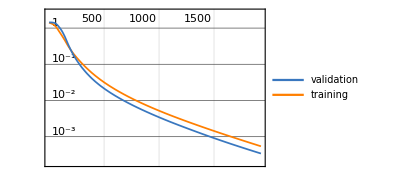
| rounds
loss | -Graphics-

<|Loss→0.000542739,ErrorRate→0.|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=2;
dataV[[n]]
netF@dataV[[n,1]]
```

d→a

a

```mathematica
Nest[#<>netF[#]&,{"ab"},12]
```

abcdabcdabcdab

### predict the next number of sequence (RNN)

#### 1 prepare datasets

```mathematica
seq=Mod[#,4]&/@Range@20;
Batch[n_]:=((Most@#->Last@#)&@(List/@Take[seq,{#,#+RandomInteger[{1,5}]}&@RandomInteger[{1,Length@seq-5}]]))&/@Range@n
```

```mathematica
Batch@2
```

{{{2},{3},{0}}→{1},{{3}}→{0}}

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
LongShortTermMemoryLayer[6],
SequenceLastLayer[],
LinearLayer[1]},
"Input"->{"Varying",1},
"Output"->1]
```

NetChain[<>]

```mathematica
net[{{2},{3}}]
```

{-0.246633}

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV];
```

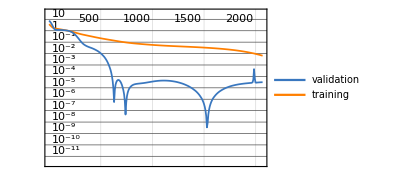
| rounds
loss | -Graphics-

<|Loss→0.00647446|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=4;
dataV[[n]]
netF@dataV[[n,1]]
```

{{1},{2},{3}}→{0}

{-0.0153329}

```mathematica
Nest[Append[#,netF[#]]&,{{1}},12]
```

{{1},{2.40696},{2.38236},{0.0918298},{1.05758},{2.16272},{2.80689},{-0.00399959},{1.13482},{2.19449},{2.70462},{0.0243514},{1.1556}}

### predict next point of graphic line (RNN)

#### 0 draw graphics

```mathematica
GT=GeometricTransformation;
ST=ScalingTransform;
TT=TranslationTransform;
RT=RotationTransform;
```

```mathematica
RandomGraphic[]:=Graphics[GT[RandomChoice[{Rectangle[#,#+RandomInteger[{1,5},2]]&@RandomInteger[{0,5},2],GT[Polygon[{{0,0},{1,1},{2,0}}],ST[RandomReal[{1.5,2.5},2]]]}],TT[RandomReal[{-5,5},2]].RT[RandomReal[{-π,π}],{0,0}]],ImageSize->256,PlotRange->{{-15,15},{-15,15}},Frame->True];
```

```mathematica
FlattenGraphics[gr_Graphics]:=Module[{gr1,gr2,gr3,gr4,gr5},gr1=Replace[gr,{Rectangle[{x1_,y1_},{x2_,y2_}]:>{Line[{{x1,y1},{x2,y1}}],Line[{{x2,y1},{x2,y2}}],Line[{{x2,y2},{x1,y2}}],Line[{{x1,y2},{x1,y1}}]},Polygon[a__]:>Line/@Partition[a,2,1,1]},All];
gr2=DeleteCases[gr1,Rotate[{{}},_,_],All];
gr3=DeleteCases[gr2,Translate[{},_],All];
gr4=Replace[List@gr3,GeometricTransformation[g__,{m__,v__}]:>Replace[g,{x_Integer|x_Real,y_Integer|y_Real}:>m.{x,y}+v,All],-1];;
gr5=Graphics[Cases[gr4,_Line,All],Options@gr]]
```

```mathematica
GraphicsTransformation2Origin[gr_]:=Module[{grF,firstLine,len,tf},firstLine=gr[[1,1,1]];
len=EuclideanDistance@@firstLine;
tf=FindGeometricTransform[{{0,0},{len,0}},firstLine][[2]];
{tf,Graphics@Replace[gr[[1]],{x_Integer|x_Real,y_Integer|y_Real}:>tf@{x,y},All]}]
```

```mathematica
GraphicsTransform2Site[gr_,tf_]:=Graphics[Replace[gr[[1]],{x_Integer|x_Real,y_Integer|y_Real}:>tf@{x,y},All],ImageSize->256,PlotRange->{{-15,15},{-15,15}},Frame->True]
```

```mathematica
Graphics2Graph[gr_Graphics]:=Module[{gr6,coords,vertices,rules,edges,graph},gr6=First@FlattenGraphics@gr;
coords=DeleteDuplicates@Cases[gr6,{x_Integer|x_Real,y_Integer|y_Real}:>1.{x,y},All];
vertices=Range@Length@coords;
rules=Thread[coords->vertices];
edges=Cases[Replace[gr6,{x_Integer|x_Real,y_Integer|y_Real}:>((1.{x,y})/.rules),All],a_Line:>DirectedEdge@@First@a,1];
graph=Graph[vertices,edges,VertexCoordinates->coords]]
```

```mathematica
Graph2Turtle[gr_Graph]:=Module[{vl,el,cl,elC,ll,al},vl=VertexList@gr;
el=List@@@EdgeList@gr;
cl=PropertyValue[gr,VertexCoordinates];
elC=Part[cl,#]&/@el;
ll=EuclideanDistance@@@elC;
al=Prepend[#[[2]]-#[[1]]&/@Partition[PlanarAngle[#[[1]]->{#[[1]]+{1,0},#[[2]]}]&/@elC,2,1],0];
Transpose[{ll,al}]]
```

```mathematica
Turtle2Graphics[tCode_]:=Module[{tPos,tAngle,tPosA},tPos={tCode[[1,1]],0};
tAngle=0;
Graphics[FoldList[(tPosA=tPos;
tAngle=tAngle+#2[[2]];
tPos=tPosA+RotationTransform[tAngle]@{#2[[1]],0};
Line[{tPosA,tPos}])&,Line[{{0,0},tPos}],Rest@tCode],Frame->True,PlotRange->10]]
```

#### 1 prepare datasets

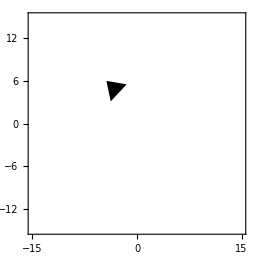

```mathematica
gr=RandomGraphic[]
```

```mathematica
Batch[n_]:=Module[{gr,tf,gr1,tur},gr=RandomGraphic[];
{tf,gr1}=GraphicsTransformation2Origin@FlattenGraphics@gr;
tur=Graph2Turtle@Graphics2Graph[gr1];
{Most@#->Last@#,tf}&@tur]&/@Range@n
```

```mathematica
Batch@3
```

{{{{3.3795,0},{3.3795,-1.53154}}→{4.87222,-2.37582},TransformationFunction[(0.493916 | -0.869509 | 2.68505
0.869509 | 0.493916 | -1.99481
0. | 0. | 1.)]},{{{2.93257,0},{2.93257,4.73511}}→{4.19412,-2.36756},TransformationFunction[(0.103673 | 0.994611 | 3.04377
-0.994611 | 0.103673 | 2.76934
0. | 0. | 1.)]},{{{2.66704,0},{2.66704,-1.25454}}→{4.31866,-2.51432},TransformationFunction[(0.127972 | -0.991778 | -1.9616
0.991778 | 0.127972 | 1.89435
0. | 0. | 1.)]}}

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

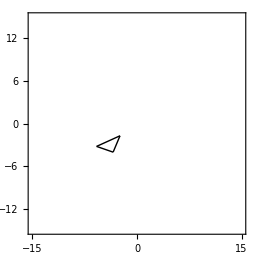

```mathematica
n=1;
que=dataV[[n,1,1]];
ans=dataV[[n,1,2]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{GatedRecurrentLayer[12],SequenceLastLayer[],LinearLayer[2]},"Input"->{"Varying",2},"Output"->{2}]
```

NetChain[<>]

```mathematica
net@dataV[[2,1,1]]
```

{0.134323,0.116633}

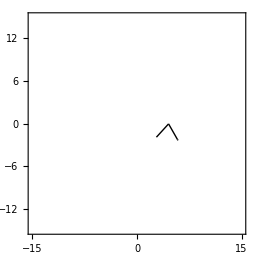

```mathematica
n=2;
que=dataV[[n,1,1]];
ans=net@dataV[[n,1,1]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```

#### 3 train and validate

```mathematica
netT=NetTrain[net,dataT[[All,1]],All,ValidationSet->dataT[[All,1]]];
```

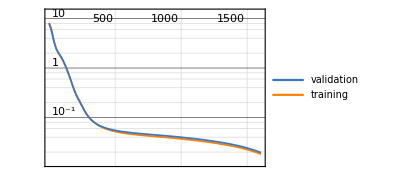
| rounds
loss | -Graphics-

<|Loss→0.01816|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=4;
dataV[[n,1]]
netF@dataV[[n,1,1]]
```

{{4.,0},{1.,1.5708},{4.,1.5708}}→{1.,1.5708}

{1.04214,1.63119}

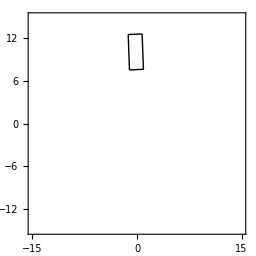

```mathematica
n=9;
que=dataV[[n,1,1]];
ans=netF@dataV[[n,1,1]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```